Example of Compton scattering calculation

**********************************************************************************************

1.Compton scattering calculation using 4 γ matrices (4*4) (conventional calculation)

f(s,u)；8 (m^4-s u+m^2 (3 s+u))

g(s,u)；8 (m^4-s u+m^2 (s+3 u))

f(u,s)；8 m^2 (2 m^2+s+u)

g(u,s)；8 m^2 (2 m^2+s+u)

Scattering cross section of laboratory system (conventional calculation)；{(0.25 w (2 w^2-w w0+2 w0^2+w w0 Cos[2 theta]))/w0^3}

γ=0.173；{(0.125 (1.45043 Cos[theta]-2.40586 (3+Cos[2 theta])+0.173 Cos[3 theta]))/(-1.173+0.173 Cos[theta])^3}

γ=0.173

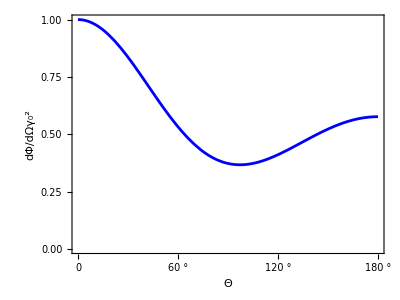

**********************************************************************************************

2.Compton scattering calculation using γ matrix (256*256)

2.1.Calculation using 4 γ matrices (256*256) under Minkowski spacetime

Calculate the metric tensor as(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

det (determinant of the metric tensor)=-1

f(s,u)；512 (m^4-s u+m^2 (3 s+u))

g(s,u)；512 (m^4-s u+m^2 (s+3 u))

f(u,s)；512 m^2 (2 m^2+s+u)

g(u,s)；512 m^2 (2 m^2+s+u)

Scattering cross section of laboratory system (consistent with conventional calculation results)；{(0.25 w (2 w^2-w w0+2 w0^2+w w0 Cos[2 theta]))/w0^3}

Same as above (when γ=0.173)；{(0.125 (1.45043 Cos[theta]-2.40586 (3+Cos[2 theta])+0.173 Cos[3 theta]))/(-1.173+0.173 Cos[theta])^3}

**********************************************************************************************

2.2.Trial calculation example using 16 γ matrices (256*256) in curved space-time

Calculate the metric tensor as (-1 | 1/999 | 1/999 | 1/999
1/999 | 1000/999 | 1/999 | 1/999
1/999 | 1/999 | 1000/999 | 1/999
1/999 | 1/999 | 1/999 | 1000/999)

det (determinant of the metric tensor)=-333667/332667

f(s,u)；((7980007911802121000000 m^6+8023980511427065864560121 m^4 s+998001 s^2 (7980007911802121 s-7984111896338000000 u)+2 m^2 s (11924209592616455593060121 s+3992055948169000000000000 u))/(15625000000000000000000 s))

g(s,u)；((15952068136315560121 m^8-119700567320357143879758 m^6 s-7992091904249802121000000 s^3 u+1000000 m^2 s^2 (7992091904249802121 s+23968119752553268330 u)+m^4 s (8047920759019647647560121 s+7948103807850113000000 u))/(15625000000000000000000 s^2))

f(u,s)；((-39916304183972593384143 m^6+15824239447735098191231714 m^4 s-103784361508242000000 s^2 u+m^2 s (7992107975706243354615857 s+8032024279890215948000000 u))/(15625000000000000000000 s))

g(u,s)；((-39916304183972593384143 m^6+15824239447735098191231714 m^4 s-103784361508242000000 s^2 u+m^2 s (7992107975706243354615857 s+8032024279890215948000000 u))/(15625000000000000000000 s))

Scattering cross section in a laboratory system (trial calculation example using 16 γ matrices (256*256) for curved space)；{1/(w0^3 (2+(w (-1+Cos[theta]))/(w-w0))^2)5.69504×10^-26 w (4 (7968151656657220338000000 w^2+7756487152969944560121 w w0+7992091904249802121000000 w0^2)+1/(w-w0)4 w (7960171536816830507000000 w^2+15987774802845509503180363 w w0-7987926211246666096115857 w0^2) (-1+Cos[theta])+1/(w-w0)^2 w (7936231177295661014000000 w^3+95824153742139871320281573 w^2 w0-119632464499484019364158570 w w0^2+32016040511572915977560121 w0^3) (-1+Cos[theta])^2+1/(w-w0)^3 w^2 (-7980119840389831000000 w^3+47880332311865183760360726 w^2 w0-79640611701156519183926856 w w0^2+31960164279816662462120242 w0^3) (-1+Cos[theta])^3+1/(w-w0)^4 3 w^3 w0 (2658692000010712105186707 w^2-5301391935797679443077238 w w0+2658692000010712105186707 w0^2) (-1+Cos[theta])^4)}

γ=0.173；{1.90285×10^-24 (7.98326×10^24+(1.07403×10^25)/(1.173-0.173 Cos[theta])^2-(2.37098×10^23)/(-1.173+0.173 Cos[theta])^3+(1.84352×10^25)/(-1.173+0.173 Cos[theta]))}

**********************************************************************************************

3.When using four γ matrices under Minkowski spacetime (conventional calculation) and γ matrix (256*256) under curved spacetime.
Comparison of trial calculation examples using 16 (trial calculation examples in this paper)

γ=0.173

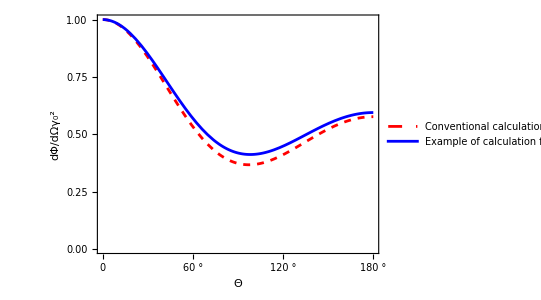

```mathematica
(*Title:Compton Scattering Calculation Author:[Hirokaxzu Maruyama] 
Date:January 2025 Description:
This code compares Compton scattering calculations using:
1. Conventional 4x4 gamma matrices 
2. Extended 256x256 gamma matrices in Minkowski spacetime 
3. Extended 256x256 gamma matrices in curved spacetime*)



(*Key Variables:m=mass 
gu[μ]=gamma matrices (upper index) 
gd[μ]=gamma matrices (lower index) 
sl[q]=Dirac slash notation for momentum q*)

(*Step 1:Calculate scattering amplitude using conventional method*)
(*Step 2:Convert to Mandelstam variables*)
(*Step 3:Calculate differential cross section*)


(*Results Interpretation:-The conventional calculation yields Klein-Nishina formula-The 256x256 calculation in Minkowski space reproduces the conventional result-The curved space calculation shows deviations due to metric effects*)

Print[Style["Example of Compton scattering calculation",Blue]];


Print["**********************************************************************************************"];
Print[Style["1.Compton scattering calculation using 4 γ matrices (4*4) (conventional calculation)",Blue]];
(*γ matrix(4×4)*)
m=.;
gu[0]={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gu[1]={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gu[2]={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gu[3]={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
e4=IdentityMatrix[4];

gd[0]=1*gu[0];
gd[1]=-gu[1];
gd[2]=-gu[2];
gd[3]=-gu[3];

sl[q]=gu[0]*q0+gu[1]*(-q1)+gu[2]*(-q2)+gu[3]*(-q3)+m*e4;
sl[p]=gu[0]*p0+gu[1]*(-p1)+gu[2]*(-p2)+gu[3]*(-p3)+m*e4;
sl[k]=gu[0]*k0+gu[1]*(-k1)+gu[2]*(-k2)+gu[3]*(-k3);
sl[j]=gu[0]*j0+gu[1]*(-j1)+gu[2]*(-j2)+gu[3]*(-j3);
ms=m*e4;

s1=0;y1=0;
s2=0;y2=0;
s3=0;y3=0;
s4=0;y4=0;

For[x=0,x≤3,x++,
For[y=0,y≤3,y++,
(*f(s,u)*)
s1=Tr[(sl[q]).gu[x].(sl[p]+sl[k]).gu[y].(sl[p]).gd[y].(sl[p]+sl[k]).gd[x]];
(*g(s,u)*)
s2=Tr[(sl[q]).gu[y].(sl[p]-sl[j]).gu[x].(sl[p]).gd[x].(sl[p]-sl[j]).gd[y]];
(*f(u,s)*)
s3=Tr[(sl[q]).gu[x].(sl[p]+sl[k]).gu[y].(sl[p]).gd[x].(sl[p]-sl[j]).gd[y]];
(*g(s,u)*)
s4=Tr[(sl[q]).gu[y].(sl[p]-sl[j]).gu[x].(sl[p]).gd[y].(sl[p]+sl[k]).gd[x]];

y1=Simplify[y1+s1,TimeConstraint->5000];
y2=Simplify[y2+s2,TimeConstraint->5000];
y3=Simplify[y3+s3,TimeConstraint->5000];
y4=Simplify[y4+s4,TimeConstraint->5000];
]];

 γ=.;
T1=Simplify[y1//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u}];(*f(s,u)*)
T2=Simplify[y2//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u}];(*g(s,u)*)
  T3=Simplify[y3//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u}];(*f(u,s)*)

T4=Simplify[y4//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u}];(*g(u,s)*)


Print["f(s,u)；",T1];
Print["g(s,u)；",T2];
Print["f(u,s)；",T3];
Print["g(u,s)；",T4];

T5=(m^2/(s-m^2)^2)*(1*(T1*(1/(s-m^2)^2)+(T3+T4)*(1/((s-m^2)*(u-m^2)))+T2*(1/(u-m^2)^2)));
 T6=Pi*T5*dt;
T7=FullSimplify[ExpandAll[T6/.s->2*m*w0+m^2/.u->-2*m*w+m^2/.dt->(1/Pi)*w^2]];
T8=T7/.Solve[(w0-w)/(w0*w)==1/m*(1-Cos[theta]),m]//Simplify;
y1=FullSimplify[T8/.w->w0*u/(u+w0(1-Cos[theta]))/.w0->γ*u/.u->m];
y2=y1/.theta->kakudo/.γ->0.173/.kakudo->0;
T9=T8/y2;
Print["Scattering cross section of laboratory system (conventional calculation)；",T9];
y3=y1/y2;
γ=0.173;
Print["γ=0.173；",y3];(*Scattering cross section for laboratory system (for γ=0.173)*)

Print["γ=0.173"];
Plot[y3,{theta,0,Pi},PlotStyle->Blue,AspectRatio->0.75,Frame->True,PlotRange->{Degree*{0,180},{0,1}},FrameLabel->{"Θ",dΦ/Labeled[dΩ,Subsuperscript["γ",0,2],Left]},FrameTicks->{{Table[{t,PaddedForm[t,{4,2}]},{t,0,1,0.25}],None},{Degree*Table[t,{t,0,180,30}],None}},GridLines->{Degree*Table[t,{t,0,180,30}],Table[t,{t,0,1,0.25}]}]


Print["**********************************************************************************************"];
Print[Style["2.Compton scattering calculation using γ matrix (256*256)",Blue]];


(*γ matrix(256×256)*)(*Find 16 combinations of γ matrices (256×256) that satisfy the anticommutative relationship*)
demoteRank4to2[y_]:=Flatten[Map[Flatten,Transpose[y,{1,3,2,4}],{2}],1];
pauli8times[g1_,g2_,g3_,g4_,g5_,g6_,g7_,g8_]:=demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,g1,g2]],demoteRank4to2[Outer[Times,g3,g4]]]],demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,g5,g6]],demoteRank4to2[Outer[Times,g7,g8]]]]]];


g[1]={{1,0},{0,-1}};
g[2]={{0,-I},{I,0}};
g[3]={{0,1},{1,0}};
g[0]={{1,0},{0,1}};

e256=IdentityMatrix[256];


γuv[0]=pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[0],g[3]];
γuv[1]=I*pauli8times[g[0],g[0],g[0],g[0],g[3],g[2],g[2],g[2]];
γuv[2]=I*pauli8times[g[0],g[0],g[0],g[1],g[2],g[2],g[2],g[2]];
γuv[3]=I*pauli8times[g[0],g[0],g[3],g[2],g[2],g[2],g[2],g[2]];

γuv[4]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[0],g[1]];
γuv[5]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[3],g[2]];
γuv[6]=I*pauli8times[g[1],g[2],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[7]=I*pauli8times[g[0],g[0],g[1],g[2],g[2],g[2],g[2],g[2]];

γuv[8]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[3],g[2],g[2]];
γuv[9]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[1],g[2]];
γuv[10]=I*pauli8times[g[3],g[2],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[11]=I*pauli8times[g[0],g[0],g[0],g[0],g[1],g[2],g[2],g[2]];

γuv[12]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[1],g[2],g[2]];
γuv[13]=I*pauli8times[g[0],g[1],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[14]=I*pauli8times[g[0],g[3],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[15]=I*pauli8times[g[0],g[0],g[0],g[3],g[2],g[2],g[2],g[2]];


num=115792089237316195423570985008687907853269984665640564039457584007913129639936;

(*Confirm determinant*)

(*16 γ matrices (256×256) Calculation to confirm that the anticommutative relationship is satisfied*)

yt=0;
For[kh=0,kh≤15,kh++,
For[ks1=0,ks1≤15,ks1++,
yf=Det[γuv[kh].γuv[ks1]+γuv[ks1].γuv[kh]];
yt=yf+yt;
If[kh=!=ks1 && yf==num*16,Print["No.",km,",x=",kh,",y=",ks1]];
]];

If[kh==16&& ks1==16 && yt/num==16,Print[""],Print["γ matrix (256*256) 16 pieces Anti-commutation relation confirmation NG"]];

(*Set weighing*)


Print[Style["2.1.Calculation using 4 γ matrices (256*256) under Minkowski spacetime",Blue]];

gd[0]=1;
gd[1]=1;
gd[2]=1;
gd[3]=1;
gd[4]=0;
gd[5]=0;
gd[6]=0;
gd[7]=0;
gd[8]=0;
gd[9]=0;
gd[10]=0;
gd[11]=0;
gd[12]=0;
gd[13]=0;
gd[14]=0;
gd[15]=0;

m256=1*m;


(*γ matrix multiplied by metric*)

For[km1=0,km1≤15,km1++,
γu[km1]=-gd[km1]*γuv[km1];
];


For[km2=0,km2≤15,km2++,
γd[km2]=1*γu[km2];
];
γd[0]=-1*γu[0];


metric={{-gd[0],gd[10],gd[12],gd[14]},{gd[11],gd[1],gd[4],gd[6]},{gd[13],gd[5],gd[2],gd[8]},{gd[15],gd[7],gd[9],gd[3]}}/gd[0];

Print["Calculate the metric tensor as",MatrixForm[metric]];

Print["det (determinant of the metric tensor)=",Det[metric]];


sl[q]=(γu[0]*q0+γu[1]*-q1+γu[2]*-q2+γu[3]*-q3+m256*e256);
sl[p]=(γu[0]*p0+γu[1]*-p1+γu[2]*-p2+γu[3]*-p3+m256*e256);
sl[k]=(γu[0]*k0+γu[1]*-k1+γu[2]*-k2+γu[3]*-k3);
sl[j]=(γu[0]*j0+γu[1]*-j1+γu[2]*-j2+γu[3]*-j3);





s10=0;y10=0;
s20=0;y20=0;
s30=0;y30=0;
s40=0;y40=0;


For[x=0,x≤3,x++,
For[y=0,y≤3,y++,
(*f(s,u)*)
s10=Tr[(sl[q]).γu[x].(sl[p]+sl[k]).γu[y].(sl[p]).γd[y].(sl[p]+sl[k]).γd[x]];
(*g(s,u)*)
s20=Tr[(sl[q]).γu[y].(sl[p]-sl[j]).γu[x].(sl[p]).γd[x].(sl[p]-sl[j]).γd[y]];
(*f(u,s)*)
s30=Tr[(sl[q]).γu[x].(sl[p]+sl[k]).γu[y].(sl[p]).γd[x].(sl[p]-sl[j]).γd[y]];
(*g(u,s)*)
s40=Tr[(sl[q]).γu[y].(sl[p]-sl[j]).γu[x].(sl[p]).γd[y].(sl[p]+sl[k]).γd[x]];

y10=Simplify[y10+s10,TimeConstraint->5000];
y20=Simplify[y20+s20,TimeConstraint->5000];
y30=Simplify[y30+s30,TimeConstraint->5000];
y40=Simplify[y40+s40,TimeConstraint->5000];
]];




(*Conversion using Mandelstam variables*)

 γ=.;
T10=Simplify[y10/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];
T20=Simplify[y20/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];
T30=Simplify[y30/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];
T40=Simplify[y40/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];


Print["f(s,u)；",T10];
Print["g(s,u)；",T20];
Print["f(u,s)；",T30];
Print["g(u,s)；",T40];



T50=(m^2/(s-m^2)^2)*(1*(T10*(1/(s-m^2)^2)+(T30+T40)*(1/((s-m^2)*(u-m^2)))+T20*(1/(u-m^2)^2)));
 T60=Pi*T50*dt;
T70=FullSimplify[ExpandAll[T60/.s->2*m*w0+m^2/.u->-2*m*w+m^2/.dt->(1/Pi)*w^2]];
T80=T70/.Solve[(w0-w)/(w0*w)==1/m*(1-Cos[theta]),m]//Simplify;
y10=FullSimplify[T80/.w->w0*u/(u+w0(1-Cos[theta]))/.w0->γ*u/.u->m];
y20=y10/.theta->kakudo/.γ->0.173/.kakudo->0;
T90=T80/y20;
Print["Scattering cross section of laboratory system (consistent with conventional calculation results)；",T90];
y30=y10/y20;
γ=0.173;
Print["Same as above (when γ=0.173)；",y30];



Print["**********************************************************************************************"];

Print[Style["2.2.Trial calculation example using 16 γ matrices (256*256) in curved space-time",Blue]];


gd[0]=999/1000;
gd[1]=1;
gd[2]=1;
gd[3]=1;
gd[4]=1/1000;
gd[5]=1/1000;
gd[6]=1/1000;
gd[7]=1/1000;
gd[8]=1/1000;
gd[9]=1/1000;
gd[10]=1/1000;
gd[11]=1/1000;
gd[12]=1/1000;
gd[13]=1/1000;
gd[14]=1/1000;
gd[15]=1/1000;

m256=1*m;




(*γ matrix multiplied by metric*)

For[km1=0,km1≤15,km1++,
γu[km1]=-gd[km1]*γuv[km1];
];


For[km2=0,km2≤15,km2++,
γd[km2]=1*γu[km2];
];
γd[0]=-1*γu[0];


metric={{-gd[0],gd[10],gd[12],gd[14]},{gd[11],gd[1],gd[4],gd[6]},{gd[13],gd[5],gd[2],gd[8]},{gd[15],gd[7],gd[9],gd[3]}}/gd[0];

Print["Calculate the metric tensor as ",MatrixForm[metric]];

Print["det (determinant of the metric tensor)=",Det[metric]];



s100=0;y100=0;
s200=0;y200=0;
s300=0;y300=0;
s400=0;y400=0;

sl[q]=(γu[0]*q0+γu[1]*-q1+γu[2]*-q2+γu[3]*-q3+m256*e256);
sl[p]=(γu[0]*p0+γu[1]*-p1+γu[2]*-p2+γu[3]*-p3+m256*e256);
sl[k]=(γu[0]*k0+γu[1]*-k1+γu[2]*-k2+γu[3]*-k3);
sl[j]=(γu[0]*j0+γu[1]*-j1+γu[2]*-j2+γu[3]*-j3);

For[x=0,x≤15,x++,
For[y=0,y≤15,y++,
(*f(s,u)*)
s100=Tr[(sl[q]).γu[x].(sl[p]+sl[k]).γu[y].(sl[p]).γd[y].(sl[p]+sl[k]).γd[x]];
(*g(s,u)*)
s200=Tr[(sl[q]).γu[y].(sl[p]-sl[j]).γu[x].(sl[p]).γd[x].(sl[p]-sl[j]).γd[y]];
(*f(u,s)*)
s300=Tr[(sl[q]).γu[x].(sl[p]+sl[k]).γu[y].(sl[p]).γd[x].(sl[p]-sl[j]).γd[y]];
(*g(u,s)*)
s400=Tr[(sl[q]).γu[y].(sl[p]-sl[j]).γu[x].(sl[p]).γd[y].(sl[p]+sl[k]).γd[x]];

y100=Simplify[y100+s100,TimeConstraint->5000];
y200=Simplify[y200+s200,TimeConstraint->5000];
y300=Simplify[y300+s300,TimeConstraint->5000];
y400=Simplify[y400+s400,TimeConstraint->5000];
]];

(*Conversion using Mandelstam variables*)


 γ=.;
T100=Simplify[y100/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];
T200=Simplify[y200/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];
T300=Simplify[y300/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];
T400=Simplify[y400/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2)/(2 Sqrt[s]),p3->(s-m^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 m^2-s-u},TimeConstraint->5000];


Print["f(s,u)；",T100];
Print["g(s,u)；",T200];
Print["f(u,s)；",T300];
Print["g(u,s)；",T400];


T500=(m^2/(s-m^2)^2)*(1*(T100*(1/(s-m^2)^2)+(T300+T400)*(1/((s-m^2)*(u-m^2)))+T200*(1/(u-m^2)^2)));
 T600=Pi*T500*dt;
T700=FullSimplify[ExpandAll[T600/.s->2*m*w0+m^2/.u->-2*m*w+m^2/.dt->(1/Pi)*w^2]];
T800=T700/.Solve[(w0-w)/(w0*w)==1/m*(1-Cos[theta]),m]//Simplify;
y100=FullSimplify[T800/.w->w0*u/(u+w0(1-Cos[theta]))/.w0->γ*u/.u->m];
y200=y100/.theta->kakudo/.γ->0.173/.kakudo->0;
T900=T800/y200;
Print["Scattering cross section in a laboratory system (trial calculation example using 16 γ matrices (256*256) for curved space)；",T900];
γ=0.173;
y300=y100/y200;
Print["γ=0.173；",y300];



Print["**********************************************************************************************"];

Print[Style["3.When using four γ matrices under Minkowski spacetime (conventional calculation) and γ matrix (256*256)\ under curved spacetime.
Comparison of trial calculation examples using 16 (trial calculation examples in this paper)",Blue]];
Print["γ=0.173"];

Plot[{y30,y300},{theta,0,Pi},PlotStyle->{{Red,Dashed},Blue},AspectRatio->0.75,Frame->True,
PlotRange->{Degree*{0,180},{0,1}},PlotLegends->Placed[LineLegend[Automatic,{"Conventional calculation","Example of calculation for this paper"},LabelStyle->8,
LegendFunction->(Framed[#,Background->Opacity[4/4,White]]&),LegendLayout->"Column"],{{0.987,0.955},{1,0.9}}],FrameLabel->{"Θ",dΦ/Labeled[dΩ,Subsuperscript["γ",0,2],Left]},FrameTicks->{{Table[{t,PaddedForm[t,{4,2}]},{t,0,1,0.25}],None},{Degree*Table[t,{t,0,180,30}],None}},
GridLines->{Degree*Table[t,{t,0,180,30}],Table[t,{t,0,1,0.25}]}]
```